# 01 Loading Continuous Data

XXXX.

Load Neuralynx ncs files

```mathematica
<<NounouW`
```

HokahokaW`
Thu 4 Aug 2016 10:52:14     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Artifact info as of: Tue 2 Aug 2016 08:45:33
     Local repo path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [ada9721f7ce16dc5c1a303a892475b6cbf3373e7]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

NounouW`
Thu 4 Aug 2016 10:52:15     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Git info loaded: Thu 4 Aug 2016 10:52:15
     Local repo path:   C:\Users\ktakagaki\prog\_w\NounouW\.git
     Current branch [hash]:  dev [c6fa48445eaa327d13d379f0ef7b3853f71ee9ea]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

The starting point is to have some continuous data files:

```mathematica
tempFiles=FileNames["S:\\VSDdata\\proj.SPP\\data\\SPP.Nlx2\\SPP067\\2016-07-07_15-10-56\\*.ncs"][[4;;7]]
```

{S:\VSDdata\proj.SPP\data\SPP.Nlx2\SPP067\2016-07-07_15-10-56\CSC13.ncs,S:\VSDdata\proj.SPP\data\SPP.Nlx2\SPP067\2016-07-07_15-10-56\CSC14.ncs,S:\VSDdata\proj.SPP\data\SPP.Nlx2\SPP067\2016-07-07_15-10-56\CSC15.ncs,S:\VSDdata\proj.SPP\data\SPP.Nlx2\SPP067\2016-07-07_15-10-56\CSC16.ncs}

We can now use the standard function NNLoad to load the contents of these files into a data object (actually, a java object for nounou, the Java/Scala package which underlies NounouW).

Note, for large files such as these *.ncs files, nounou will not load all of the data into memory. Instead, it will load file pointers and file information (e.g. sampling rate, etc.) in a way that the data can be streamed rapidly from disk.

```mathematica
tempJavaDataObject=NNLoad[ tempFiles ]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

Now, we can interact with this Java object to access information, or to call specific segments of data.

```mathematica
NNPrintInfo[ tempJavaDataObject, "Timing"]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	  61212160 ( 31:52.88) (  1912.9)	  2984886413 ( 0:00.00)

This call was directly equivalent with a direct call to the java object like this:

```mathematica
tempJavaDataObject@timing[]@toStringFull[]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	  61212160 ( 31:52.88) (  1912.9)	  2984886413 ( 0:00.00)

Of note here:

The Mathematica Java calling syntax is modified from Java (e.g. using @ and []), in order to avoid pre-defined definitions in Mathematica for Java symbols such as . . The above input in native Java would be tempJavaDataObject.timing().toStringFull().

The Java method toStringFull() returns a Java string, which Mathematica automatically converts to a Mathematica string. The same type of conversion is done for numerical values (including BigIntegerand breeze.Complex) and Arrays of numerical or string values (to Mathematica List[] objects). See the Mathematica JLink guidehttps://reference.wolfram.com/language/JLink/tutorial/CallingJavaFromTheWolframLanguage.html for the full syntax of calling JVM functions from Mathematica.

You can access data from this object using the following NounouW command:

```mathematica
tempData=NNReadTrace[ 
(*1*) tempJavaDataObject,  (*2*) Range[0,3], (*3*) {0 ;; 10, 0}];
Dimensions[tempData]
```

{4,11}

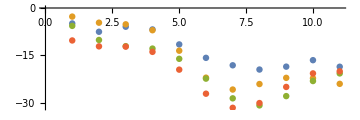

```mathematica
ListPlot[tempData, AspectRatio-> 1/3, ImageSize-> Medium]
```

(*1*) The first argument is naturally the Java data object.

(*2*) The next argument specifies data channels to read. Note above that we have specified channels [0 to 3] above. Since we loaded 4 *.ncs files, we have 4 channels which we can call, and since nounou (and Java in general) is zero-indexed, we need to call channels [0 to 3].

(*3*) The third argument is a time specification. Here, we call data sample numbers 0 to 10, from segment 0. For more information regarding specifying timing (for example, specifying in frames, in timestamps, or in ms) see the help file for NNReadTrace.